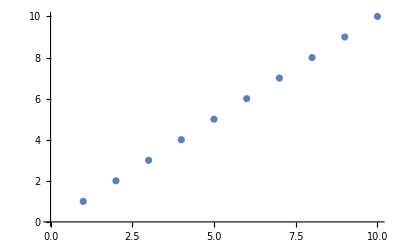

```mathematica
ListPlot[Range[10]]
```

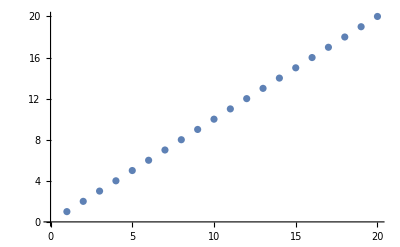

```mathematica
ListPlot[Range[20]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/stnav/Projects/test

```mathematica
list = RunProcess[{"git", "status", "-s"},"StandardOutput"]
paths= Map[(StringSplit[#," "]&)/*(Part[#,2]&),StringSplit[list,"\n"]]
paths =Select[paths,StringEndsQ[#,".nb"]&]

Map[
Export["Rendered/"<>(StringReplace[#,".nb"->".pdf"]),Import[#]]&,paths ]
```

M sample.nb
?? Renderedsample.pdf
?? nbgitconvert
?? output.pdf

{sample.nb,Renderedsample.pdf,nbgitconvert,output.pdf}

{sample.nb}

{Rendered/sample.pdf}

```mathematica
list = RunProcess[{"git", "diff", "--cached", "--name-status"},"StandardOutput"]
paths= Map[(StringSplit[#,"\t"]&),StringSplit[list,"\n"]]
paths =Select[paths,#[[1]]!="D"&&StringEndsQ[#[[2]],".nb"]&]
paths =paths[[;;,2]]

Map[
Export["Rendered/"<>(StringReplace[#,".nb"->".pdf"]),Import[#]]&,paths ]
Run[{"git", "add", "*.pdf"}]
```

A	nbgitconvert
D	out.pdf
M	sample.nb

{{A,nbgitconvert},{D,out.pdf},{M,sample.nb}}

{{M,sample.nb}}

{sample.nb}

```mathematica
"a"=="a"
```

True